0.000863

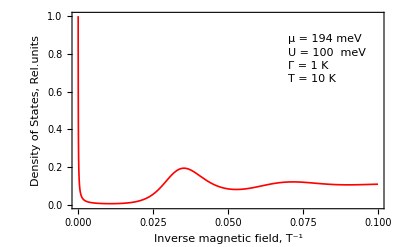

```mathematica
t=0.4; c=6.25;a1=0.00125; G1=0.0000863; b=0.0004138; 
d=0.12; mu2=0.1937; mu3=0.113; T=0.000863

f5[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2/2-√((t^2+4*U^2)*(a1*n1/x)+4*U^2*d^2+2*t^2*d*U+t^4/4));
F3[x_,n1_,U_]=(1/((mu2-f5[x,n1,U])^2+G1^2))*(1+(3.14*T)^2/(6)*(6*(mu2-f5[x,n1,U])^2-2*G1^2)/(((mu2-f5[x,n1,U])^2+G1^2))^2);
F4[x_,U_]=b*G1*Sum[F3[x,n1,U],{n1,0,100}]*(1/x);
Plot[F4[x,-0.1],{x,0,0.1},PlotRange->{0,1},PlotStyle->{{Thickness[0.003],Red}},FrameLabel->{Style["Inverse magnetic field, T^-1",10],Style["Density of States, Rel.units",10]},Epilog->{{Black,Text["μ = 194 meV",{0.07,0.85},{-1,-1}]},{Black,Text["U = 100  meV",{0.07,0.78},{-1,-1}]},{Black,Text["Γ = 1 K",{0.07,0.71},{-1,-1}]},{Black,Text["T = 10 K",{0.07,0.64},{-1,-1}]}},Frame->True]
```

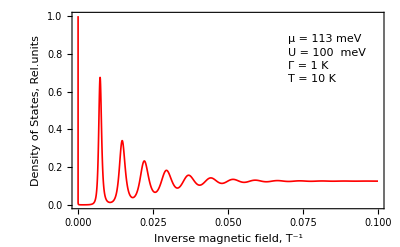

```mathematica
f6[x_,n1_,U_]:=√(d^2+U^2+(a1*n1/x)+t^2-2*√((t^2+U^2)*(a1*n1/x)+U^2*d^2));
F5[x_,n1_,U_]=(1/((mu3-f6[x,n1,U])^2+G1^2))*(1+(3.14*T)^2/(6)*(6*(mu3-f6[x,n1,U])^2-2*G1^2)/(((mu3-f6[x,n1,U])^2+G1^2))^2);
F6[x_,U_]=b*G1*Sum[F5[x,n1,U],{n1,0,100}]*(1/x);
Plot[F6[x,-0.1],{x,0,0.1},PlotRange->{0,1},PlotStyle->{{Thickness[0.003],Red}},FrameLabel->{Style["Inverse magnetic field, T^-1",10],Style["Density of States, Rel.units",10]},Epilog->{{Black,Text["μ = 113 meV",{0.07,0.85},{-1,-1}]},{Black,Text["U = 100  meV",{0.07,0.78},{-1,-1}]},{Black,Text["Γ = 1 K",{0.07,0.71},{-1,-1}]},{Black,Text["T = 10 K",{0.07,0.64},{-1,-1}]}},Frame->True]
```

```mathematica
Plot[{F4[x,-0.1],F6[x,-0.1]},{x,0,0.1},PlotRange->{0,1},PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Blue}},Epilog->{{Black,Text["AB, μ = 194 meV",{0.07,0.85},{-1,-1}]},{Black,Text["AA, μ = 113 meV",{0.07,0.78},{-1,-1}]},{Black,Text["U = 100  meV",{0.0765,0.71},{-1,-1}]},{Black,Text["Γ = 1 K",{0.0765,0.64},{-1,-1}]},{Black,Text["T = 10 K",{0.0765,0.57},{-1,-1}]}},FrameLabel->{Style["Inverse magnetic field, T^-1",10],Style["Density of States, Rel.units",10]},Frame->True]
```